```mathematica
Expression Mathématica
```

```mathematica
a+b//FullForm
```

Plus[a,b]

```mathematica
a-c//FullForm
```

Plus[a,Times[-1,c]]

```mathematica
a*c//FullForm
```

Times[a,c]

```mathematica
a/c//FullForm
```

Times[a,Power[c,-1]]

```mathematica
1/2//FullForm
```

Rational[1,2]

```mathematica
a*x^2+b*x+c//FullForm
```

Plus[c,Times[b,x],Times[a,Power[x,2]]]

```mathematica
{1,2,3}//FullForm
```

List[1,2,3]

```mathematica
If[x≥0,x,-x]//FullForm
```

If[GreaterEqual[x,0],x,Times[-1,x]]

```mathematica
1+1//FullForm
```

2

```mathematica
Hold[1+1]//FullForm
```

Hold[Plus[1,1]]

```mathematica
"Tous les objets de Mathématica sont construits sur le même modèle. TOUT est expression!"
```

```mathematica
Hold[f[x]/;x<3:=x^2]//FullForm
```

Hold[SetDelayed[Condition[f[x],Less[x,3]],Power[x,2]]]

```mathematica
Hold[f[x]/;x≤3:=x^2]//FullForm
```

Hold[SetDelayed[Condition[f[x],LessEqual[x,3]],Power[x,2]]]

```mathematica
Hold[f[x]/;x==3:=x^2]//FullForm
```

Hold[SetDelayed[Condition[f[x],Equal[x,3]],Power[x,2]]]

```mathematica
Hold[f[x]/;x≤3=x^2]//FullForm
```

Hold[Set[Condition[f[x],LessEqual[x,3]],Power[x,2]]]

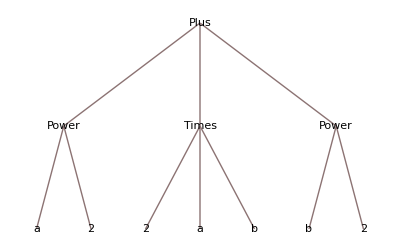

```mathematica
a^2+2*a*b+b^2//TreeForm
```

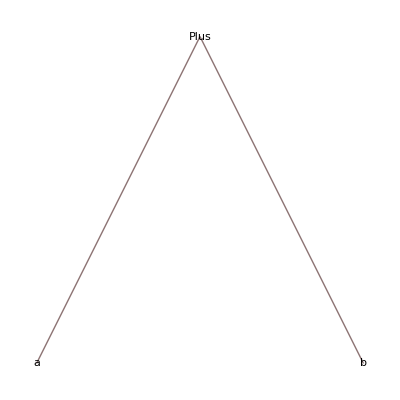

```mathematica
a+b//TreeForm
```

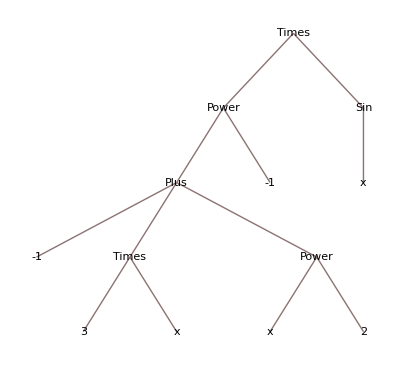

```mathematica
Sin[x]/(x^2+3*x-1)//TreeForm
```

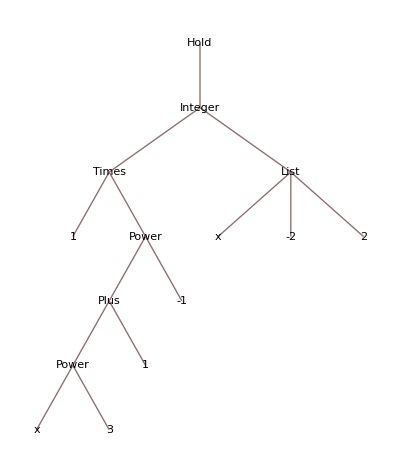

```mathematica
Hold[Integer[1/(x^3+1),{x,-2,2}]]//TreeForm
```

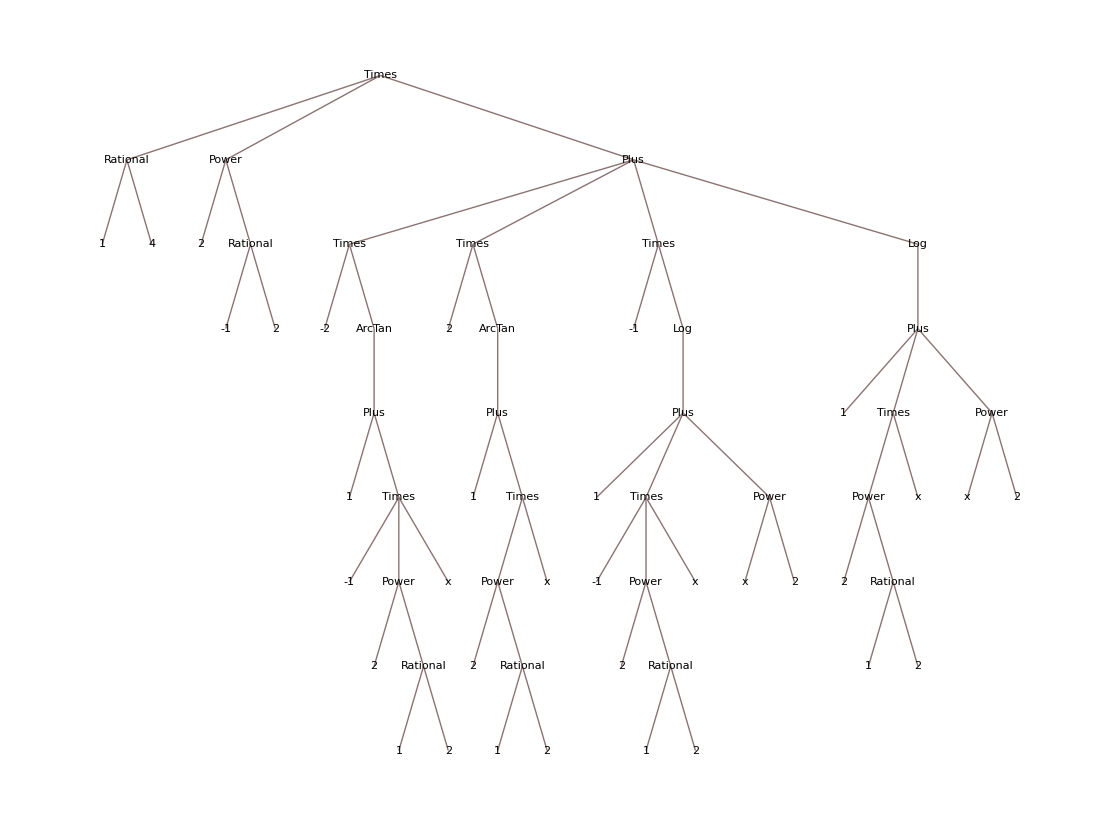

```mathematica
Integrate[1/(x^4+1),x]//TreeForm
```

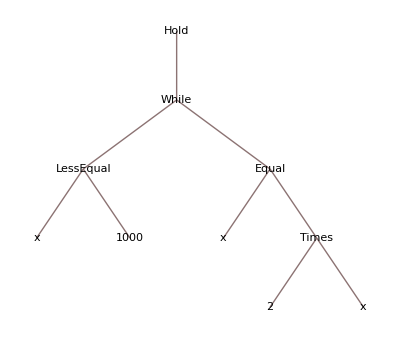

```mathematica
Hold[While[x≤1000,x==2*x]]//TreeForm
```

```mathematica
L={1,4,{2,6},{7,4,{1,8}},11,0};
```

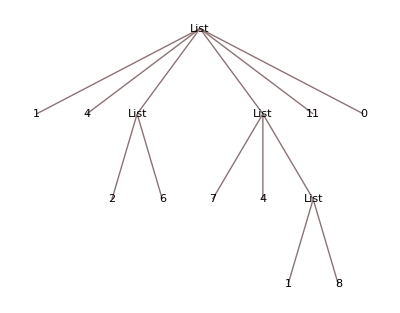

```mathematica
L//TreeForm
```

```mathematica
Length[L]
```

6

```mathematica
Depth[L]
```

4

```mathematica
L[[4]]
```

{7,4,{1,8}}

```mathematica
L[[4,3]]
```

{1,8}

```mathematica
L[[4,3,2]]
```

8

```mathematica
e=(a+Sin[b+c])^Sqrt[3];
```

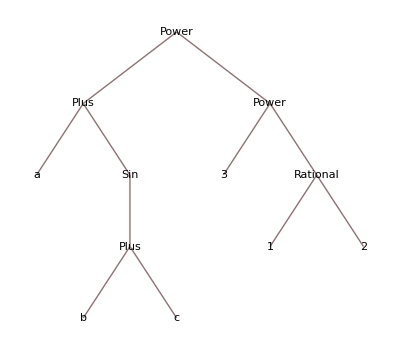

```mathematica
e//TreeForm
```

```mathematica
Length[e]
```

2

```mathematica
Depth[e]
```

5

```mathematica
e[[1]]
```

a+Sin[b+c]

```mathematica
e[[1,2]]
```

Sin[b+c]

```mathematica
e[[1,2,1]]
```

b+c

```mathematica
e[[1,2,1,2]]
```

c

```mathematica
Clear[e]
```

```mathematica
e=a+b;
```

```mathematica
Head[e]
```

Plus

```mathematica
Head[{1,2,3}]
```

List

```mathematica
Head[5/9]
```

Rational

```mathematica
Head[1]
```

Integer

```mathematica
Head[1.]
```

Real

```mathematica
Head[Pi]
```

Symbol

```mathematica
Head[Sin[x]/x]
```

Times

```mathematica
Head[Sin[#]/#&]
```

Function

```mathematica
Head[Sin]
```

Symbol